| Estimate | Standard Error | t-Statistic | P-Value
Ref | 6.78519 | 0.207804 | 32.6519 | 5.05837×10^-22

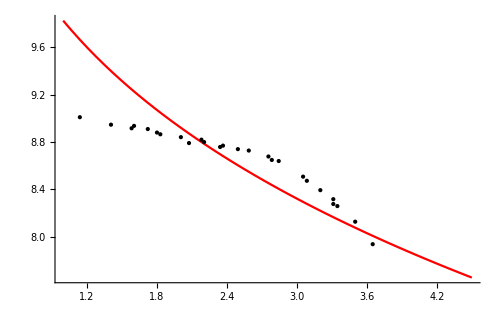

```mathematica
SetDirectory[NotebookDirectory[]];
data=Import["noyola.dat"];
L=Length[data];
Ie=1000;
Ip[R_]:=Log[Ie*Exp[-7.669*((R/Ref)^0.25-1.0)]]
(*Plot[Log[Ip[R]],{R,0,12}]*)
fit = NonlinearModelFit[data,Ip[R],{Ref},R,MaxIterations->1000];
(*fit//Normal//InputForm*)
(*fit["BestFit"]*)
fit["ParameterTable"]
Plot[fit[R],{R,1,4.5},PlotStyle->Red,Epilog:>Point[data],ImageSize->500]
```